```mathematica
SetDirectory[NotebookDirectory[]]
rasterizeBackground[g_,res_: 100]:=Show[Graphics[{Inset[Rasterize[Show[g,ImagePadding->0,ImageMargins->0,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],PlotRangeClipping->False],ImageResolution->res],Scaled[{0,0}],Scaled[{0,0}],Scaled[1]]}],Sequence@@Options[g],Sequence@@Options[g,PlotRange],Sequence@@Options[g,Epilog]];
Clear[Δ]
Clear[ω]
dispersion=Solve[0==Det[{{-ω^2+I*η*ω+2*κ+1/(1+Δ),2*κ*(1-Δ)/(1+Δ)*Cos[q/2]},{2*κ*(1+Δ)/(1-Δ)*Cos[q/2],-ω^2+I*η*ω+2*κ+1/(1-Δ)}}],ω];
spring[p0_,p1_,divs_,height_]:=Module[{L,xhat,yhat},L=Norm[p1-p0]; xhat=(p1-p0)/L; yhat={xhat[[2]],-xhat[[1]]};Join[{p0,p0+L/divs*xhat},Table[p0+i*L/divs*xhat+height*yhat*(-1)^i,{i,2,divs-2}],{p1-L/divs*xhat,p1}]];
ωmin=3.3;
ωmax=3.7;
Amin=0.0;
Amax=0.08;
Npoints=100;
M=32;
M2=3;
κ=1;
η=0.1;
cf[x_]:=Lighter[Blend[{Yellow,Red},(x-0.45)/(0.7-0.45)]]
cf[x_]:=Lighter[Red]

M2=3;
A1[a_,ω_,Δ_,q_]:=ArrayFlatten[Table[((1+(-1)^i*Δ)*(-ω^2))*KroneckerDelta[i,j]*KroneckerDelta[n,m],{n,-M2,M2},{m,-M2,M2},{i,1,2},{j,1,2}]];
A2[a_,ω_,Δ_,q_]:=ArrayFlatten[Table[((1+(-1)^i*Δ)*(-ω^2*2*n+I*ω*η))*KroneckerDelta[i,j]*KroneckerDelta[n,m],{n,-M2,M2},{m,-M2,M2},{i,1,2},{j,1,2}]];
A3[a_,ω_,Δ_,q_]:=ArrayFlatten[Table[((1+(-1)^i*Δ)*(-ω^2*n^2+I*ω*η*n+2*κ)+1)*KroneckerDelta[i,j]*KroneckerDelta[n,m]-κ*(1-(-1)^i*Δ)*(KroneckerDelta[i,1]*KroneckerDelta[j,2]+Exp[I*q]*KroneckerDelta[i,2]*KroneckerDelta[j,1])*KroneckerDelta[n,m]-κ*(1-(-1)^i*Δ)*(Exp[-I*q]*KroneckerDelta[i,1]*KroneckerDelta[j,2]+KroneckerDelta[i,2]*KroneckerDelta[j,1])*KroneckerDelta[n,m]+a*ω^2/2*(KroneckerDelta[n+1,m]+KroneckerDelta[n-1,m])*KroneckerDelta[i,j],{n,-M2,M2},{m,-M2,M2},{i,1,2},{j,1,2}]];
A[a_,ω_,Δ_,q_]:=ArrayFlatten[{{A3[a,ω,Δ,q],A2[a,ω,Δ,q]},{ConstantArray[0,{2*(2*M2+1),2*(2*M2+1)}],IdentityMatrix[2*(2*M2+1)]}}]
B[a_,ω_,Δ_,q_]:=ArrayFlatten[{{ConstantArray[0,{2*(2*M2+1),2*(2*M2+1)}],-A1[a,ω,Δ,q]},{IdentityMatrix[2*(2*M2+1)],ConstantArray[0,{2*(2*M2+1),2*(2*M2+1)}]}}]
A4[ω_,Δ_,q_,ϵ_]:=ArrayFlatten[Table[((1+(-1)^i*Δ)*(-ω^2*(ϵ+n)^2+I*ω*η*(ϵ+n)+2*κ)+1)*KroneckerDelta[i,j]*KroneckerDelta[n,m]-κ*(1-(-1)^i*Δ)*(KroneckerDelta[i,1]*KroneckerDelta[j,2]+Exp[I*q]*KroneckerDelta[i,2]*KroneckerDelta[j,1])*KroneckerDelta[n,m]-κ*(1-(-1)^i*Δ)*(Exp[-I*q]*KroneckerDelta[i,1]*KroneckerDelta[j,2]+KroneckerDelta[i,2]*KroneckerDelta[j,1])*KroneckerDelta[n,m],{n,-M2,M2},{m,-M2,M2},{i,1,2},{j,1,2}]];
B4[ω_]:=ArrayFlatten[Table[-ω^2/2*(KroneckerDelta[n+1,m]+KroneckerDelta[n-1,m])*KroneckerDelta[i,j],{n,-M2,M2},{m,-M2,M2},{i,1,2},{j,1,2}]];
```

/home/zack/oscillators/anharmonic

## Direct simulations

```mathematica
filebase="data/subharmonic";
{M,freq,amp,dt, eta, epsilon, delta, cycles, seed, step}=Import[filebase<>"out.dat"][[2]]
dat=Partition[BinaryReadList[filebase<>"dat.npy","Real64"][[17;;-1]],2*M];
Dimensions[dat]
norms=Total/@Abs[dat[[All,1;;32]]]^2/M;
max=Max[Mod[dat[[-500;;-1,1;;32]]+Pi,2*Pi]-Pi]
min=Min[Mod[dat[[-500;;-1,1;;32]]+Pi,2*Pi]-Pi]
cf[x_]:=ColorData["TemperatureMap"][(x-min)/(max-min)];
Grid[{{ListPlot[Log[norms],Joined->True,ImageSize->300,ImageSize->300],ListPlot[{dat[[-500;;-1,1]],Cos[2*Pi*dt*Range[500]]},PlotRange->All,Joined->True,ImageSize->300],ListDensityPlot[Mod[dat[[1;;-1;;2*Round[1/dt],1;;M]]+Pi,2*Pi]-Pi,ImageSize->500,AspectRatio->1,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False,PlotRange->All,InterpolationOrder->0]}}]
```

{32,2.,0.12,0.05,0.1,0.,0.5,5000.,1,1}

{100000,64}

0.46477

-0.46477

-Graphics- | -Graphics- | -Graphics-

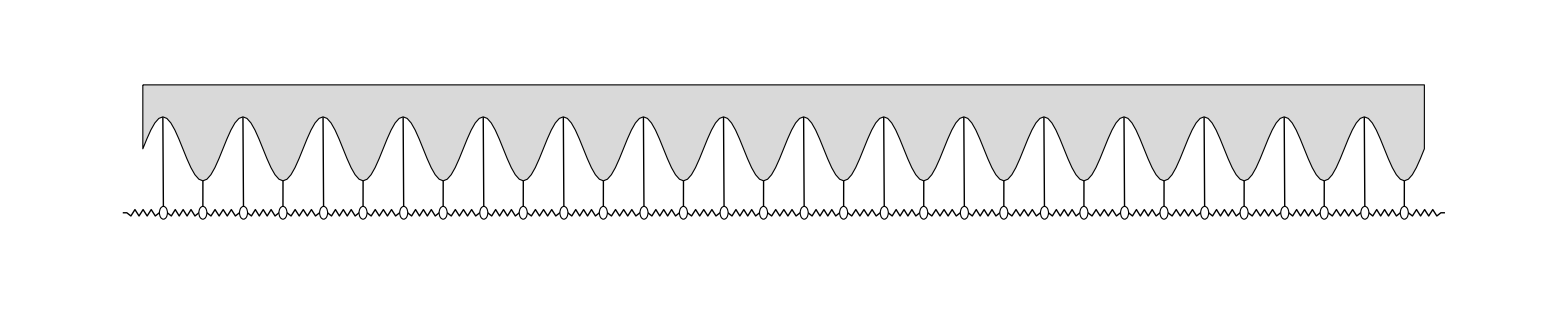

springs.pdf

```mathematica
n=-20;
dx=1;
lengths=Riffle[ConstantArray[delta,M/2],ConstantArray[-delta,M/2]];
thetas=dat[[n,1;;M]];
f[x_]:=-delta*Cos[Pi*x/dx];
t=n*2*Pi*0.05/freq;
z0={0,amp*Cos[freq*t]};
p0=Graphics[{Table[Line[{z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*i,1+lengths[[i]]}}],{i,1,M}],Table[Line[spring[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*(i+1),1+lengths[[i+1]]} -(1+ lengths[[i+1]])*{Sin[thetas[[i+1]]],Cos[thetas[[i+1]]]},10,0.05]],{i,1,M-1}],Line[spring[z0+{dx*M,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx*(M+1),1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],Line[spring[z0+{0,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],EdgeForm[Black],White,Table[Disk[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},0.1],{i,1,M}],LightGray,Polygon[Join[{{dx/2,z0[[2]]+2}},Table[{x,z0[[2]]+1+f[x]},{x,dx*1/2,dx*(M+1/2),dx/10}],{{dx*(M+1/2),z0[[2]]+2},{dx/2,z0[[2]]+2}}]]},ImageSize->2000,PlotRange->{dx*{1/2+0.01,M+1/2+0.01},{-1,3}}]
Export["springs.pdf",p0]
```

```mathematica
p=Show[Block[{Δ=0},ListPlot[{Table[{q,Re[ω/.dispersion[[2]]]},{q,0,Pi,Pi/50}],Table[{q,Re[ω/.dispersion[[4]]]},{q,0,Pi,Pi/50}]},Joined->True,PlotStyle->Directive[Black,AbsoluteThickness[2],Dashed],Axes->False,Frame->True,FrameLabel->{k,ω},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->2/5,PlotRange->{1/2,5/2},FrameTicks->{{Table[{i,PaddedForm[i,{2,1}]},{i,0.5,2.5,0.5}],Table[{i,""},{i,0.5,2.5,0.5}]},{{{0,0},{π/4,DisplayForm[RowBox[{"π","/",8}]]},{π/2,DisplayForm[RowBox[{"π","/",4}]]},{(3 π)/4,DisplayForm[RowBox[{3"π","/",8}]]},{π,DisplayForm[RowBox[{"π","/",2}]]}},Table[{i,""},{i,0,Pi,Pi/4}]}}]],Block[{Δ=0.5},ListPlot[{Table[{q,Re[ω/.dispersion[[2]]]},{q,0,Pi,Pi/50}],Table[{q,Re[ω/.dispersion[[4]]]},{q,0,Pi,Pi/50}]},Joined->True,PlotStyle->Directive[Black,AbsoluteThickness[2]]]],ImageSize->{Automatic,200}]
Export["dispersion.pdf",p]
```

-Graphics-

dispersion.pdf

## Floquet exponents

```mathematica
ω=3.4;
Δ=0.5;
q=0;
a=0.05;
{evals,evecs}=Eigensystem[{A[a,ω,Δ,q],B[a,ω,Δ,q]}];
evals
Grid[{{ListPlot[{Re[#],ω*Im[#]}&/@Eigenvalues[{A[a,ω,0,q],B[a,ω,0,q]}],PlotRange->{{0,1},All},ImageSize->300],ListPlot[{Re[#],ω*Im[#]}&/@Eigenvalues[{A[a,ω,Δ/2,q],B[a,ω,Δ/2,q]}],PlotRange->{{0,1},All},ImageSize->300],ListPlot[{Re[#],ω*Im[#]}&/@Eigenvalues[{A[a,ω,Δ,q],B[a,ω,Δ,q]}],PlotRange->{{0,1},All},ImageSize->300]}}]
val=evals[[-1]];
vec=evecs[[-1,1;;2*(2*M2+1)]];
val^2*A1[a,ω,Δ,q].vec+val*A2[a,ω,Δ,q].vec+A3[a,ω,Δ,q].vec
```

{3.68646+0.0147059 ⅈ,-3.68646+0.0147059 ⅈ,-3.32624+0.0147059 ⅈ,3.32624+0.0147059 ⅈ,2.67729+0.0303916 ⅈ,-2.67729+0.0303916 ⅈ,2.67729-0.000979861 ⅈ,-2.67729-0.000979861 ⅈ,2.32347+0.0301381 ⅈ,-2.32347+0.0301381 ⅈ,2.32347-0.00072629 ⅈ,-2.32347-0.00072629 ⅈ,1.67679+0.0300567 ⅈ,-1.67679+0.0300567 ⅈ,-1.67679-0.000644919 ⅈ,1.67679-0.000644919 ⅈ,1.32321+0.0300566 ⅈ,-1.32321+0.0300566 ⅈ,-1.32321-0.000644814 ⅈ,1.32321-0.000644814 ⅈ,-0.676792+0.0300566 ⅈ,0.676792+0.0300566 ⅈ,0.676792-0.000644802 ⅈ,-0.676792-0.000644802 ⅈ,-0.323208+0.0300566 ⅈ,0.323208+0.0300566 ⅈ,-0.323208-0.000644802 ⅈ,0.323208-0.000644802 ⅈ}

-Graphics- | -Graphics- | -Graphics-

{1.02012×10^-13-3.13623×10^-14 ⅈ,-3.11115×10^-13+2.08981×10^-13 ⅈ,6.96665×10^-15-2.2142×10^-14 ⅈ,6.51076×10^-14+1.04482×10^-14 ⅈ,-4.44089×10^-15-1.77636×10^-14 ⅈ,-2.22045×10^-15-3.27516×10^-14 ⅈ,-9.99201×10^-16+3.94129×10^-15 ⅈ,2.66454×10^-15-4.16334×10^-15 ⅈ,2.66454×10^-15-1.04083×10^-16 ⅈ,9.08995×10^-16-2.07473×10^-15 ⅈ,7.00395×10^-16+1.40946×10^-17 ⅈ,7.60744×10^-16-3.73901×10^-16 ⅈ,-1.08166×10^-16+1.12794×10^-15 ⅈ,5.48535×10^-16-8.18268×10^-16 ⅈ}

### Individual parameters

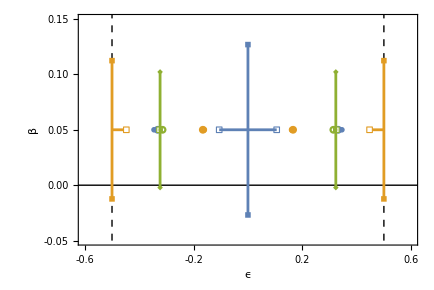

```mathematica
Clear[ω]
ωd=1.0;
Δ=0.5;
amin=0.01;
amax=0.8;
q=0;
evals1=Cases[Eigenvalues[{A[amin,ωd,Δ,q],B[amin,ωd,Δ,q]}],u_/;Re[u]>-0.5&&Re[u]<0.5];
evals2=Cases[Eigenvalues[{A[amax,ωd,Δ,q],B[amax,ωd,Δ,q]}],u_/;Re[u]>-0.5&&Re[u]<0.5];
p1=Show[ListPlot[{{Re[#],ωd*Im[#]}&/@evals1[[1;;2]],{Re[#],ωd*Im[#]}&/@evals1[[3;;4]],{Re[#],ωd*Im[#]}&/@evals2[[1;;2]],{Re[#],ωd*Im[#]}&/@evals2[[3;;4]]},PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},ImageSize->300,Axes->False,Frame->True,FrameLabel->{"ϵ","β"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Prolog->{Line[{{-1,0},{1,0}}],Dashed,Line[{{0.5,-η/2},{0.5,2*η}}],Line[{{-0.5,-η/2},{-0.5,2*η}}]},PlotStyle->Directive[ColorData[97,"ColorList"][[1]],PointSize[0.04]],PlotMarkers->{Graphics[{Circle[{0,0},0.02]},PlotRange->{-1,1}],Graphics[{EdgeForm[ColorData[97,"ColorList"][[1]]], White, Rectangle[{-0.02,-0.02},{0.02,0.02}]},PlotRange->{-1,1}],Graphics[{Disk[{0,0},0.05]},PlotRange->{-1,1}],Graphics[{Rectangle[{-0.05,-0.05},{0.05,0.05}]},PlotRange->{-1,1}]},ImageSize->300,ImagePadding->{{75,10},{75,10}},AspectRatio->1],ListPlot[{{Re[#],ωd*Im[#]}&/@evals1[[3;;4]],{Re[#],ωd*Im[#]}&/@evals2[[3;;4]]},Joined->True,PlotStyle->Directive[ColorData[97,"ColorList"][[1]],AbsoluteThickness[2]],PlotRange->{{-0.6,0.6},{-η/2,1.5*η}}]];
ωd=2.0;
amin=0.01;
amax=0.12;
evals1=Cases[Eigenvalues[{A[amin,ωd,Δ,q],B[amin,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
evals2=Cases[Eigenvalues[{A[amax,ωd,Δ,q],B[amax,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
p2=Show[ListPlot[{{Re[#],ωd*Im[#]}&/@evals1[[1;;2]],{Re[#],ωd*Im[#]}&/@evals1[[3;;4]],{Re[#],ωd*Im[#]}&/@evals2[[1;;2]],{Re[#],ωd*Im[#]}&/@evals2[[3;;4]],{Re[#],ωd*Im[#]}&/@evals2[[5;;6]]},PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},ImageSize->300,Axes->False,Frame->True,FrameLabel->{"ϵ","β"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Prolog->{Line[{{-1,0},{1,0}}],Dashed,Line[{{0.5,-η/2},{0.5,2*η}}],Line[{{-0.5,-η/2},{-0.5,2*η}}]},PlotStyle->Directive[ColorData[97,"ColorList"][[2]],PointSize[0.04]],PlotMarkers->{Graphics[{EdgeForm[ColorData[97,"ColorList"][[2]]],White,Rectangle[{-0.02,-0.02},{0.02,0.02}]},PlotRange->{-1,1}],Graphics[{Circle[{0,0},0.02]},PlotRange->{-1,1}],Graphics[{Rectangle[{-0.05,-0.05},{0.05,0.05}]},PlotRange->{-1,1}],Graphics[{Rectangle[{-0.05,-0.05},{0.05,0.05}]},PlotRange->{-1,1}],Graphics[{EdgeForm[ColorData[97,"ColorList"][[2]]],Disk[{0,0},0.05]},PlotRange->{-1,1}]},ImageSize->300,ImagePadding->{{75,10},{75,10}},AspectRatio->1],ListPlot[{{Re[#],ωd*Im[#]}&/@evals2[[{2,3}]],{Re[#],ωd*Im[#]}&/@evals2[[{1,4}]],{{Re[#],ωd*Im[#]},{0.5,ωd*Im[#]}}&@evals1[[1]],{{Re[#],ωd*Im[#]},{-0.5,ωd*Im[#]}}&@evals1[[2]]},PlotStyle->Directive[ColorData[97,"ColorList"][[2]],AbsoluteThickness[2]],PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},Joined->True]];
ωd=3.4;
amin=0.0;
amax=0.05;
evals1=Cases[Eigenvalues[{A[amin,ωd,Δ,q],B[amin,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
evals2=Cases[Eigenvalues[{A[amax,ωd,Δ,q],B[amax,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
p3=Show[ListPlot[{{Re[#],ωd*Im[#]}&/@evals1[[1;;2]],{Re[#],ωd*Im[#]}&/@evals1[[3;;4]],{Re[#],ωd*Im[#]}&/@evals2[[1;;2]],{Re[#],ωd*Im[#]}&/@evals2[[3;;4]]},PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},ImageSize->300,Axes->False,Frame->True,FrameLabel->{"ϵ","β"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Prolog->{Line[{{-1,0},{1,0}}],Dashed,Line[{{0.5,-η/2},{0.5,2*η}}],Line[{{-0.5,-η/2},{-0.5,2*η}}]},PlotStyle->Directive[ColorData[97,"ColorList"][[3]],PointSize[0.04]],PlotMarkers->{Graphics[{EdgeForm[ColorData[97,"ColorList"][[3]]],White,Rectangle[{-0.02,-0.02},{0.02,0.02}]},PlotRange->{-1,1}],Graphics[{Circle[{0,0},0.02]},PlotRange->{-1,1}],Graphics[{Polygon[2^(1/2)*{{0,0.05},{0.05,0},{0,-0.05},{-0.05,0}}]},PlotRange->{-1,1}],Graphics[{Polygon[2^(1/2)*{{0,0.05},{0.05,0},{0,-0.05},{-0.05,0}}]},PlotRange->{-1,1}]},ImageSize->300,ImagePadding->{{75,10},{75,10}},AspectRatio->1],ListPlot[{{Re[#],ωd*Im[#]}&/@evals1[[{1,3}]],{Re[#],ωd*Im[#]}&/@evals1[[{2,4}]],{Re[#],ωd*Im[#]}&/@evals2[[{2,4}]],{Re[#],ωd*Im[#]}&/@evals2[[{1,3}]]},PlotStyle->Directive[ColorData[97,"ColorList"][[3]],AbsoluteThickness[2]],PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},Joined->True]];
p1=Show[p1,p2,p3,AspectRatio->2/3,ImageSize->435,ImagePadding->{{75,15},{75,15}},FrameTicks->{{Table[{i,PaddedForm[N[i],{3,2}]},{i,-0.05,0.15,0.05}],Table[{i,""},{i,-0.05,0.15,0.05}]},{Table[{i,PaddedForm[N[i],{2,1}]},{i,-6/10,6/10,2/10}],Table[{i,""},{i,-6/10,6/10,2/10}]}}]
```

```mathematica
ωd=3.4;
AbsoluteTiming[Monitor[test1=Table[Eigenvalues[{A4[ωd,0,0,ϵ],B4[ωd]}],{ϵ,0,1,0.002}];,ϵ]]
AbsoluteTiming[Monitor[test2=Table[Eigenvalues[{A4[ωd,Δ,0,ϵ],B4[ωd]}],{ϵ,0,1,0.002}];,ϵ]]
AbsoluteTiming[Monitor[test3=Table[Eigenvalues[{A4[ωd,0,Pi,ϵ],B4[ωd]}],{ϵ,0,1,0.002}];,ϵ]]
AbsoluteTiming[Monitor[test4=Table[Eigenvalues[{A4[ωd,Δ,Pi,ϵ],B4[ωd]}],{ϵ,0,1,0.002}];,ϵ]]
```

{1.34381,Null}

{1.41996,Null}

{1.47567,Null}

{1.50998,Null}

```mathematica
p2=Grid[{{ListPlot[Join[Transpose[{Im[#],Abs[Re[#]]}&/@#&/@(Cases[#,u_/;Re[u]>0.0][[1;;2]]&/@test1[[2;;-1,-4;;-1]])],Transpose[{Im[#],Abs[Re[#]]}&/@#&/@(Cases[#,u_/;Re[u]>0.0][[1;;2]]&/@test3[[2;;-1,-4;;-1]])]],Joined->True,Frame->True,Axes->False,FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{Im[Subscript[A,d]],Re[Subscript[A,d]]},FrameTicks->{{Table[{i,PaddedForm[i,{3,2}]},{i,0,0.31,0.05}],Table[{i,""},{i,0,0.3,0.05}]},{Table[{i,PaddedForm[i,{2,1}]},{i,-0.4,0.4,0.2}],Table[{i,""},{i,-0.4,0.4,0.2}]}},LabelStyle->Directive[16,Black],AspectRatio->1,ImageSize->250,PlotRange->{{-0.5,0.5},{0,0.3}},ImagePadding->{{75,15},{50,15}}],ListPlot[Join[Transpose[{Im[#],Abs[Re[#]]}&/@#&/@(Cases[#,u_/;Re[u]>0.0][[1;;2]]&/@test2[[2;;-1,-4;;-1]])],Transpose[{Im[#],Abs[Re[#]]}&/@#&/@(Cases[#,u_/;Re[u]>0.0][[1;;2]]&/@test4[[2;;-1,-4;;-1]])]],Joined->True,Frame->True,Axes->False,FrameStyle->Directive[Black,AbsoluteThickness[2]],FrameLabel->{Im[Subscript[A,d]],None},FrameTicks->{{Table[{i,""},{i,0,0.3,0.05}],Table[{i,""},{i,0,0.3,0.05}]},{Table[{i,PaddedForm[i,{2,1}]},{i,-0.4,0.4,0.2}],Table[{i,""},{i,-0.4,0.4,0.2}]}},LabelStyle->Directive[16,Black],AspectRatio->1,ImageSize->185,PlotRange->{{-0.5,0.5},{0,0.301}},ImagePadding->{{15,15},{50,15}}]}}];
p=Grid[{{p1},{p2}}]
Export["floquet.pdf",p]
```

-Graphics-
-Graphics- | -Graphics-

floquet.pdf

### Large sweep

```mathematica
M=100;
Δ=0.5;
ωmin=0.5;
ωmax=5.0;
amin=0;
amax=1.0;
num=250;AbsoluteTiming[Monitor[vals1=N[{#[[1]],#[[2]],2*Im[#[[3,2]]],Re[#[[3,2]]],#[[3,1]]}]&/@Flatten[Table[{ω,a,First[MinimalBy[Flatten[ParallelTable[Cases[Transpose[{ConstantArray[q,4*(2*M2+1)],Eigenvalues[{A[a,ω,Δ,q],B[a,ω,Δ,q]}]}],u_/;Re[u[[2]]]>-0.01&&Re[u[[2]]]≤0.51],{q,0,Pi,4*Pi/M}],1],Im[#[[2]]]&]]},{ω,ωmin,ωmax,(ωmax-ωmin)/num},{a,amin,amax,(amax-amin)/num}],1];,{(a-amin)/(amax-amin),(ω-ωmin)/(ωmax-ωmin)}]]
```

```mathematica
M=100;
Δ=0.5;
ωmin=3.0;
ωmax=4.0;
amin=0;
amax=0.1;
num=250;
AbsoluteTiming[Monitor[vals2=N[{#[[1]],#[[2]],2*Im[#[[3,2]]],Re[#[[3,2]]],#[[3,1]]}]&/@Flatten[Table[{ω,a,First[MinimalBy[Flatten[ParallelTable[Cases[Transpose[{ConstantArray[q,4*(2*M2+1)],Eigenvalues[{A[a,ω,Δ,q],B[a,ω,Δ,q]}]}],u_/;Re[u[[2]]]>-0.01&&Re[u[[2]]]≤0.51],{q,0,Pi,4*Pi/M}],1],Im[#[[2]]]&]]},{ω,ωmin,ωmax,(ωmax-ωmin)/num},{a,amin,amax,(amax-amin)/num}],1];,{(a-amin)/(amax-amin),(ω-ωmin)/(ωmax-ωmin)}]]
```

{5203.84,Null}

{4648.25,Null}

```mathematica
M=100;
Δ=0.5;
ωmin=1.0;
ωmax=3.0;
amin=0;
amax=0.25;
num=250;
AbsoluteTiming[Monitor[vals3=N[{#[[1]],#[[2]],2*Im[#[[3,2]]],Re[#[[3,2]]],#[[3,1]]}]&/@Flatten[Table[{ω,a,First[MinimalBy[Flatten[ParallelTable[Cases[Transpose[{ConstantArray[q,4*(2*M2+1)],Eigenvalues[{A[a,ω,Δ,q],B[a,ω,Δ,q]}]}],u_/;Re[u[[2]]]>-0.01&&Re[u[[2]]]≤0.51],{q,0,Pi,4*Pi/M}],1],Im[#[[2]]]&]]},{ω,ωmin,ωmax,(ωmax-ωmin)/num},{a,amin,amax,(amax-amin)/num}],1];,{(a-amin)/(amax-amin),(ω-ωmin)/(ωmax-ωmin)}]]
```

{2267.16,Null}

```mathematica
Export["data/vals1.dat",vals1]
Export["data/vals2.dat",vals2]
Export["data/vals3.dat",vals3]
```

data/vals1.dat

data/vals2.dat

data/vals3.dat

```mathematica
filebase="data/anharmonic";
{M,freq,amp,dt, eta, epsilon, delta, cycles, seed, step}=Import[filebase<>"out.dat"][[2]]
dat1=Partition[BinaryReadList[filebase<>"dat.npy","Real64"][[17;;-1]],2*M];
filebase="data/noisy";
dat2=Partition[BinaryReadList[filebase<>"dat.npy","Real64"][[17;;-1]],2*M];

Clear[t];
p1=ListPlot[{Transpose[{dt*Range[500],dat1[[-500;;-1,1]]}],Transpose[{dt*Range[500],dat1[[-500;;-1,2]]}]},PlotRange->All,Joined->True,Axes->False,Frame->True,PlotStyle->{Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[3]]],Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[2]]]},FrameLabel->{DisplayForm[RowBox[{HoldForm[Subscript[ω,d]*t],"/",2π}]],DisplayForm[RowBox[{Style[Subscript[ϕ,0],ColorData[97,"ColorList"][[2]]],", ",Style[Subscript[ϕ,1],ColorData[97,"ColorList"][[3]]]}]]},FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[Black,16],ImagePadding->{{65,15},{65,10}}, ImageSize->300,AspectRatio->1/2];

n0=1000;
n2=Position[Differences[Sign[Differences[Total[Abs[#-dat1[[n0/dt]]]^2]&/@dat1]]],2][[-1,1]];
power1=Abs[Fourier[dat1[[n0/dt;;n2,1]]]];
freqs1=Range[Length[dat1[[n0/dt;;n2,1]]]]/(Length[dat1[[n0/dt+1;;n2,1]]]*dt);
power2=Abs[Fourier[dat2[[n0/dt;;n2,1]]]];
freqs2=Range[Length[dat2[[n0/dt;;n2,1]]]]/(Length[dat2[[n0/dt+1;;n2,1]]]*dt);
p2=ListLogPlot[{Transpose[{freqs2,power2}],Transpose[{freqs1,power1}]},PlotRange->{{0,1},{10^-3,10^2}},PlotStyle->{Directive[PointSize[0.0045],ColorData[97,"ColorList"][[1]]],Directive[PointSize[0.0045],ColorData[97,"ColorList"][[4]]]},Axes->False,Frame->True,FrameTicks->{{Table[{10^i,10^ToString[i]},{i,-3,2,2}],Table[{10^i,""},{i,-3,2,2}]},{Table[{i,PaddedForm[i,{2,1}]},{i,0,1,0.2}],Table[{i,""},{i,0,1,0.2}]}},FrameLabel->{DisplayForm[RowBox[{ω,"/",Subscript[ω,d]}]],S},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{65,15},{65,10}}, ImageSize->300,AspectRatio->1/2,PlotLegends->Placed[PointLegend[{ColorData[97,"ColorList"][[4]],ColorData[97,"ColorList"][[1]]},{DisplayForm[RowBox[{ϵ,"=",PaddedForm[0.,{2,1}]}]],DisplayForm[RowBox[{ϵ,"=",PaddedForm[0.1,{2,1}]}]]},LabelStyle->Directive[13]],{0.82,0.7}]];
p0=Grid[{{p1},{p2}}]
```

{32,3.4,0.05,0.05,0.1,0.,0.5,5000.,1,1}

-Graphics-
-Graphics-

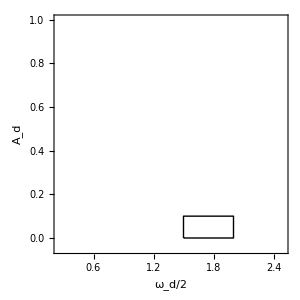
-Graphics- | -Graphics- | -Graphics-
-Graphics-

boundary.pdf

```mathematica
vals1=Import["data/vals1.dat"];
vals2=Import["data/vals2.dat"];
min=0;
max=Pi;
cf[x_]:=Lighter[ColorData["Rainbow"][0.25+0.5*(x-min)/(max-min)]];
Clear[ω]
p1=Legended[rasterizeBackground[ListDensityPlot[{#[[1]]/2,#[[2]],#[[3]]}&/@Join[#[[{1,2,5}]]&/@Cases[vals1,u_/;u[[3]]<0],{#[[1]],#[[2]],-1}&/@Cases[vals1,u_/;u[[3]]≥0]],PlotRange->{All,{-0.05,1},{0,2*Pi}},InterpolationOrder->1,ImageSize->300,ImagePadding->{{65,15},{65,10}},FrameLabel->{DisplayForm[RowBox[{Subscript[ω,d],"/",2}]],Subscript[A,d]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,ColorFunction->(cf),ColorFunctionScaling->False,Epilog->{Line[{{3/2,0},{4/2,0},{4/2,0.1},{3/2,0.1},{3/2,0}}]}]],Placed[MatrixPlot[Table[cf[Pi*(i-1)/100],{j,1,10},{i,1,100}],PlotRangePadding->None,FrameTicks->{{None,None},{None,{{1,0},{25,DisplayForm[RowBox[{π,"/",8}]]},{50,DisplayForm[RowBox[{π,"/",4}]]},{75,DisplayForm[RowBox[{3π,"/",8}]]},{100,DisplayForm[RowBox[{π,"/",2}]]}}}},LabelStyle->Directive[14,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1/10,ImageSize->{225,100},PlotLabel->k,PlotRange->{{1,10},{1,100}},DataReversed->{True,False}],Above]];
min=0.3;
max=0.5;
cf[x_]:=Blend[{Lighter[Cyan],Lighter[Orange]},(x-min)/(max-min)];
p2=Legended[rasterizeBackground[Show[ListDensityPlot[{#[[1]]/2,#[[2]],#[[3]]}&/@Join[{#[[1]],#[[2]],#[[4]]}&/@Cases[vals2,u_/;u[[3]]<0],{#[[1]],#[[2]],-1}&/@Cases[vals2,u_/;u[[3]]≥0]],PlotRange->{min-0.1,All},InterpolationOrder->1,ImageSize->300,ImagePadding->{{65,15},{65,10}},ColorFunction->cf,ColorFunctionScaling->False,AspectRatio->1,FrameLabel->{DisplayForm[RowBox[{Subscript[ω,d],"/",2}]],Subscript[A,d]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]]]]],Placed[MatrixPlot[Table[cf[min+(max-min)*(i-1)/100],{j,1,10},{i,1,100}],PlotRangePadding->None,FrameTicks->{{None,None},{None,{{1,PaddedForm[min,{3,2}]},{25,PaddedForm[min+0.25*(max-min),{3,2}]},{50,PaddedForm[min+0.5*(max-min),{3,2}]},{75,PaddedForm[min+0.75*(max-min),{3,2}]},{100,PaddedForm[max,{3,2}]}}}},LabelStyle->Directive[14,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1/10,ImageSize->{225,100},PlotLabel->ϵ,PlotRange->{{1,10},{1,100}},DataReversed->{True,False}],Above]];
p=Grid[{{p1,p2,p0}}]
Export["boundary.pdf",p]
```

## Animations

#### harmonic

```mathematica
Δ=0.5;
amin=0.01;
q=0;
dx=1;
filebase="data/harmonic";
{M,ωd,amax,dt, eta, epsilon, delta, cycles, seed, step}=Import[filebase<>"out.dat"][[2]]
dat=Partition[BinaryReadList[filebase<>"dat.npy","Real64"][[17;;-1]],2*M];
vals1=Import["data/vals1.dat"];
vals2=Import["data/vals2.dat"];
min=0;
max=Pi;
cf[x_]:=Lighter[ColorData["Rainbow"][0.25+0.5*(x-min)/(max-min)]];
amin=0.01;
evals1=Cases[Eigenvalues[{A[amin,ωd,Δ,q],B[amin,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
evals2=Cases[Eigenvalues[{A[amax,ωd,Δ,q],B[amax,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
count=0;
n0=Max[1,Length[dat]-499];
p2=Legended[rasterizeBackground[ListDensityPlot[{#[[1]]/2,#[[2]],#[[3]]}&/@Join[#[[{1,2,5}]]&/@Cases[vals1,u_/;u[[3]]<0],{#[[1]],#[[2]],-1}&/@Cases[vals1,u_/;u[[3]]≥0]],PlotRange->{All,{0,1},{0,2*Pi}},InterpolationOrder->1,ImageSize->350,ImagePadding->{{85,15},{75,10}},FrameLabel->{DisplayForm[RowBox[{Subscript[ω,d],"/",2}]],Subscript[A,d]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,ColorFunction->(cf),ColorFunctionScaling->False]],Placed[MatrixPlot[Table[cf[Pi*(i-1)/100],{j,1,10},{i,1,100}],PlotRangePadding->None,FrameTicks->{{None,None},{None,{{1,0},{25,DisplayForm[RowBox[{π,"/",8}]]},{50,DisplayForm[RowBox[{π,"/",4}]]},{75,DisplayForm[RowBox[{3π,"/",8}]]},{100,DisplayForm[RowBox[{π,"/",2}]]}}}},LabelStyle->Directive[14,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1/10,ImageSize->{225,100},PlotLabel->k,PlotRange->{{1,10},{1,100}},DataReversed->{True,False}],{0.6,1.05}]];
```

{32,1.,0.8,0.05,0.1,0.,0.5,5000.,1,1}

```mathematica
n0=Max[1,Length[dat]-500];
Monitor[AbsoluteTiming[plots1=Table[
lengths=Riffle[ConstantArray[delta,M/2],ConstantArray[-delta,M/2]];
m=(n-n0);
a=If[(n-n0)<250,amin+(amax-amin)/250*(n-n0),amax];
evals=Cases[Eigenvalues[{A[a,ωd,Δ,q],B[a,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
If[Min[Im[#]&/@evals]<0,thetas=dat[[n,1;;M]],thetas=ConstantArray[0,M]];;
f[x_]:=-delta*Cos[Pi*x/dx];
t=n*2*Pi*0.05/ωd;
z0={0,a*Cos[ωd*t]};
If[MemberQ[First/@Position[Differences[Sign[Differences[dat[[All,1]]]]],2],n],count=count+1;];
count2=Round[(n-n0)/20];
p0=Graphics[{Table[Line[{z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*i,1+lengths[[i]]}}],{i,1,M}],Table[Line[spring[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*(i+1),1+lengths[[i+1]]} -(1+ lengths[[i+1]])*{Sin[thetas[[i+1]]],Cos[thetas[[i+1]]]},10,0.05]],{i,1,M-1}],Line[spring[z0+{dx*M,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx*(M+1),1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],Line[spring[z0+{0,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],EdgeForm[Black],ColorData[97,"ColorList"][[1]],Table[Disk[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},0.1],{i,1,M}],Lighter[Red],Polygon[Join[{{dx/2,z0[[2]]+2}},Table[{x,z0[[2]]+1+f[x]},{x,dx*1/2,dx*(M+1/2),dx/10}],{{dx*(M+1/2),z0[[2]]+2},{dx/2,z0[[2]]+2}}]]},ImageSize->300,PlotRange->{dx*{1/2+0.01,4+1/2+0.01},{-2,3}}];

evals=Cases[Eigenvalues[{A[a,ωd,Δ,q],B[a,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
p1=Show[ListPlot[{{Re[#],ωd*Im[#]}&/@evals[[1;;2]],{Re[#],ωd*Im[#]}&/@evals[[3;;4]]},PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},ImageSize->350,ImagePadding->{{85,15},{75,10}},Axes->False,Frame->True,FrameLabel->{"ϵ","β"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Prolog->{Line[{{-1,0},{1,0}}],Dashed,Line[{{0.5,-η/2},{0.5,2*η}}],Line[{{-0.5,-η/2},{-0.5,2*η}}]},PlotStyle->Directive[ColorData[97,"ColorList"][[1]],PointSize[0.08]],PlotMarkers->{Graphics[{Disk[{0,0},0.05]},PlotRange->{-1,1}],Graphics[{Rectangle[{-0.05,-0.05},{0.05,0.05}]},PlotRange->{-1,1}]},ImageSize->300,ImagePadding->{{75,10},{75,10}},AspectRatio->1],ListPlot[{{Re[#],ωd*Im[#]}&/@evals1[[{3,4}]],{Re[#],ωd*Im[#]}&/@evals2[[{3,4}]]},PlotStyle->Directive[ColorData[97,"ColorList"][[1]],AbsoluteThickness[2]],PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},Joined->True]];
p=Grid[{{p0,Spacer[50],Show[p2,ListPlot[{{ωd/2,a}},PlotStyle->Directive[ColorData[97,"ColorList"][[1]],PointSize[0.04]]]],Spacer[50],p1}},Alignment->Bottom],{n,n0,Length[dat]}];],{N[(n-n0)/(1+Length[dat]-n0)],p}]
plots1[[-1]]
```

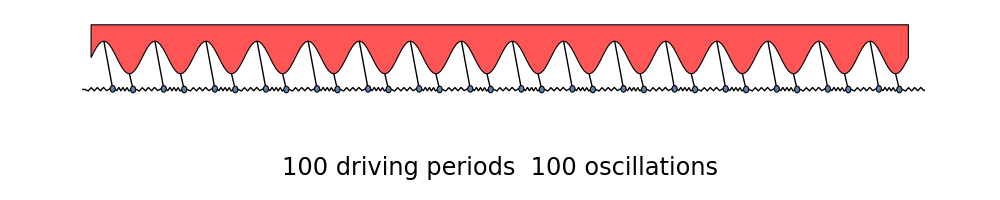

```mathematica
count=0;
n0=Max[1,Length[dat]-2000];
Monitor[AbsoluteTiming[plots2=Table[
lengths=Riffle[ConstantArray[delta,M/2],ConstantArray[-delta,M/2]];
thetas=dat[[n,1;;M]];
f[x_]:=-delta*Cos[Pi*x/dx];
t=n*2*Pi*0.05/ωd;
z0={0,amax*Cos[ωd*t]};
If[MemberQ[First/@Position[Differences[Sign[Differences[dat[[All,1]]]]],2],n],count=count+1;];
count2=Round[(n-n0)/20];
p=Graphics[{Table[Line[{z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*i,1+lengths[[i]]}}],{i,1,M}],Table[Line[spring[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*(i+1),1+lengths[[i+1]]} -(1+ lengths[[i+1]])*{Sin[thetas[[i+1]]],Cos[thetas[[i+1]]]},10,0.05]],{i,1,M-1}],Line[spring[z0+{dx*M,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx*(M+1),1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],Line[spring[z0+{0,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],EdgeForm[Black],ColorData[97,"ColorList"][[1]],Table[Disk[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},0.1],{i,1,M}],Lighter[Red],Polygon[Join[{{dx/2,z0[[2]]+2}},Table[{x,z0[[2]]+1+f[x]},{x,dx*1/2,dx*(M+1/2),dx/10}],{{dx*(M+1/2),z0[[2]]+2},{dx/2,z0[[2]]+2}}]],Black, Text[Style[ToString[count2]<>" driving periods  "<>ToString[count]<>" oscillations",24],Scaled[{0.5,0.1}]]},ImageSize->1000,PlotRange->{dx*{1/2+0.01,M+1/2+0.01},{-2,3}}],{n,n0,Length[dat]}]],{N[(n-n0)/(1+Length[dat]-n0)],p}];
plots2[[-1]]
```

```mathematica
If[!DirectoryQ[filebase<>"animation/1/"],CreateDirectory[filebase<>"animation/1/"]]
If[!DirectoryQ[filebase<>"animation/2/"],CreateDirectory[filebase<>"animation/2/"]]
AbsoluteTiming[ParallelDo[Export[filebase<>"animation/1/"<>IntegerString[n,10,4]<>".png",plots1[[n]]], {n,1,Length[plots1]}]]
AbsoluteTiming[ParallelDo[Export[filebase<>"animation/2/"<>IntegerString[n,10,4]<>".png",plots2[[n]]], {n,1,Length[plots2]}]]
```

{35.0142,Null}

{28.9694,Null}

#### subharmonic

```mathematica
Δ=0.5;
amin=0.01;
q=0;
dx=1;
filebase="data/subharmonic";
{M,ωd,amax,dt, eta, epsilon, delta, cycles, seed, step}=Import[filebase<>"out.dat"][[2]]
dat=Partition[BinaryReadList[filebase<>"dat.npy","Real64"][[17;;-1]],2*M];
vals1=Import["data/vals1.dat"];
vals2=Import["data/vals2.dat"];
vals3=Import["data/vals3.dat"];
min=0;
max=Pi;
cf[x_]:=Lighter[ColorData["Rainbow"][0.25+0.5*(x-min)/(max-min)]];
evals1=Cases[Eigenvalues[{A[amin,ωd,Δ,q],B[amin,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
evals2=Cases[Eigenvalues[{A[amax,ωd,Δ,q],B[amax,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
count=0;
n0=Max[1,Length[dat]-499];
p2=Legended[rasterizeBackground[ListDensityPlot[{#[[1]]/2,#[[2]],#[[3]]}&/@Join[#[[{1,2,5}]]&/@Cases[vals3,u_/;u[[3]]<0],{#[[1]],#[[2]],-1}&/@Cases[vals3,u_/;u[[3]]≥0]],PlotRange->{All,{-0.05,0.2},{0,2*Pi}},InterpolationOrder->1,ImageSize->350,ImagePadding->{{85,15},{75,10}},FrameLabel->{DisplayForm[RowBox[{Subscript[ω,d],"/",2}]],Subscript[A,d]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,ColorFunction->(cf),ColorFunctionScaling->False]],Placed[MatrixPlot[Table[cf[Pi*(i-1)/100],{j,1,10},{i,1,100}],PlotRangePadding->None,FrameTicks->{{None,None},{None,{{1,0},{25,DisplayForm[RowBox[{π,"/",8}]]},{50,DisplayForm[RowBox[{π,"/",4}]]},{75,DisplayForm[RowBox[{3π,"/",8}]]},{100,DisplayForm[RowBox[{π,"/",2}]]}}}},LabelStyle->Directive[14,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1/10,ImageSize->{225,100},PlotLabel->k,PlotRange->{{1,10},{1,100}},DataReversed->{True,False}],{0.6,1.05}]];
```

{32,2.,0.12,0.05,0.1,0.,0.5,5000.,1,1}

{105.723,Null}

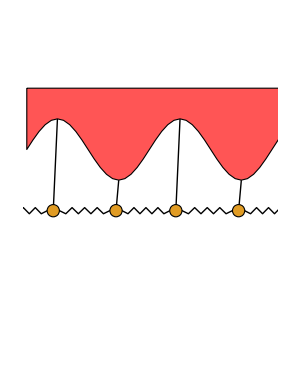
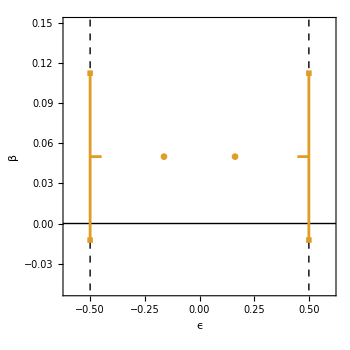
-Graphics- |  | -Graphics- |  | -Graphics-

```mathematica
n0=Max[1,Length[dat]-500];
Monitor[AbsoluteTiming[plots1=Table[
lengths=Riffle[ConstantArray[delta,M/2],ConstantArray[-delta,M/2]];
m=(n-n0);
a=If[(n-n0)<250,amin+(amax-amin)/250*(n-n0),amax];
evals=Cases[Eigenvalues[{A[a,ωd,Δ,q],B[a,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
If[Min[Im[#]&/@evals]<0,thetas=dat[[n,1;;M]],thetas=ConstantArray[0,M]];;
f[x_]:=-delta*Cos[Pi*x/dx];
t=n*2*Pi*0.05/ωd;
z0={0,a*Cos[ωd*t]};
If[MemberQ[First/@Position[Differences[Sign[Differences[dat[[All,1]]]]],2],n],count=count+1;];
count2=Round[(n-n0)/20];
p0=Graphics[{Table[Line[{z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*i,1+lengths[[i]]}}],{i,1,M}],Table[Line[spring[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*(i+1),1+lengths[[i+1]]} -(1+ lengths[[i+1]])*{Sin[thetas[[i+1]]],Cos[thetas[[i+1]]]},10,0.05]],{i,1,M-1}],Line[spring[z0+{dx*M,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx*(M+1),1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],Line[spring[z0+{0,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],EdgeForm[Black],ColorData[97,"ColorList"][[2]],Table[Disk[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},0.1],{i,1,M}],Lighter[Red],Polygon[Join[{{dx/2,z0[[2]]+2}},Table[{x,z0[[2]]+1+f[x]},{x,dx*1/2,dx*(M+1/2),dx/10}],{{dx*(M+1/2),z0[[2]]+2},{dx/2,z0[[2]]+2}}]]},ImageSize->300,PlotRange->{dx*{1/2+0.01,4+1/2+0.01},{-2,3}}];

evals=Cases[Eigenvalues[{A[a,ωd,Δ,q],B[a,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
p1=Show[ListPlot[If[Length[evals]<6,{{Re[#],ωd*Im[#]}&/@evals[[{3,4}]],{Re[#],ωd*Im[#]}&/@evals[[{1,2}]]},{{Re[#],ωd*Im[#]}&/@evals[[5;;6]],{Re[#],ωd*Im[#]}&/@evals[[1;;2]],{Re[#],ωd*Im[#]}&/@evals[[3;;4]]}],PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},ImageSize->350,ImagePadding->{{85,15},{75,10}},Axes->False,Frame->True,FrameLabel->{"ϵ","β"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Prolog->{Line[{{-1,0},{1,0}}],Dashed,Line[{{0.5,-η/2},{0.5,2*η}}],Line[{{-0.5,-η/2},{-0.5,2*η}}]},PlotStyle->Directive[ColorData[97,"ColorList"][[2]],PointSize[0.08]],PlotMarkers->{Graphics[{EdgeForm[ColorData[97,"ColorList"][[2]]],Disk[{0,0},0.05]},PlotRange->{-1,1}],Graphics[{Rectangle[{-0.05,-0.05},{0.05,0.05}]},PlotRange->{-1,1}],Graphics[{Rectangle[{-0.05,-0.05},{0.05,0.05}]},PlotRange->{-1,1}]},ImageSize->300,ImagePadding->{{75,10},{75,10}},AspectRatio->1],ListPlot[{{Re[#],ωd*Im[#]}&/@evals2[[{2,3}]],{Re[#],ωd*Im[#]}&/@evals2[[{1,4}]],{{Re[#],ωd*Im[#]},{0.5,ωd*Im[#]}}&@evals1[[1]],{{Re[#],ωd*Im[#]},{-0.5,ωd*Im[#]}}&@evals1[[2]]},PlotStyle->Directive[ColorData[97,"ColorList"][[2]],AbsoluteThickness[2]],PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},Joined->True]];
p=Grid[{{p0,Spacer[50],Show[p2,ListPlot[{{ωd/2,a}},PlotStyle->Directive[ColorData[97,"ColorList"][[2]],PointSize[0.04]]]],Spacer[50],p1}},Alignment->Bottom],{n,n0,Length[dat]}];],{N[(n-n0)/(1+Length[dat]-n0)],p}]
plots1[[-1]]
```

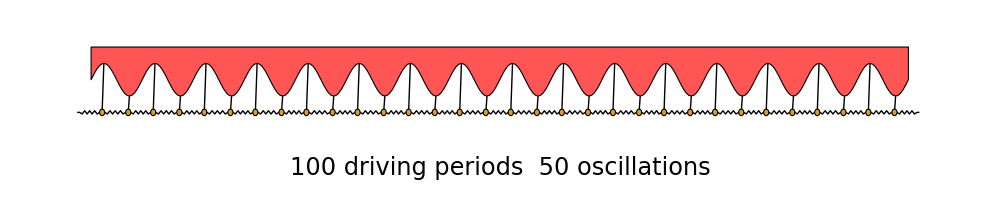

```mathematica
count=0;
n0=Max[1,Length[dat]-2000];
Monitor[AbsoluteTiming[plots2=Table[
lengths=Riffle[ConstantArray[delta,M/2],ConstantArray[-delta,M/2]];
thetas=dat[[n,1;;M]];
f[x_]:=-delta*Cos[Pi*x/dx];
t=n*2*Pi*0.05/ωd;
z0={0,amax*Cos[ωd*t]};
If[MemberQ[First/@Position[Differences[Sign[Differences[dat[[All,1]]]]],2],n],count=count+1;];
count2=Round[(n-n0)/20];
p=Graphics[{Table[Line[{z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*i,1+lengths[[i]]}}],{i,1,M}],Table[Line[spring[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*(i+1),1+lengths[[i+1]]} -(1+ lengths[[i+1]])*{Sin[thetas[[i+1]]],Cos[thetas[[i+1]]]},10,0.05]],{i,1,M-1}],Line[spring[z0+{dx*M,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx*(M+1),1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],Line[spring[z0+{0,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],EdgeForm[Black],ColorData[97,"ColorList"][[2]],Table[Disk[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},0.1],{i,1,M}],Lighter[Red],Polygon[Join[{{dx/2,z0[[2]]+2}},Table[{x,z0[[2]]+1+f[x]},{x,dx*1/2,dx*(M+1/2),dx/10}],{{dx*(M+1/2),z0[[2]]+2},{dx/2,z0[[2]]+2}}]],Black, Text[Style[ToString[count2]<>" driving periods  "<>ToString[count]<>" oscillations",24],Scaled[{0.5,0.1}]]},ImageSize->1000,PlotRange->{dx*{1/2+0.01,M+1/2+0.01},{-2,3}}],{n,n0,Length[dat]}]],{N[(n-n0)/(1+Length[dat]-n0)],p}];
plots2[[-1]]
```

```mathematica
If[!DirectoryQ[filebase<>"animation/1/"],CreateDirectory[filebase<>"animation/1/"]]
If[!DirectoryQ[filebase<>"animation/2/"],CreateDirectory[filebase<>"animation/2/"]]
AbsoluteTiming[ParallelDo[Export[filebase<>"animation/1/"<>IntegerString[n,10,4]<>".png",plots1[[n]]], {n,1,Length[plots1]}]]
AbsoluteTiming[ParallelDo[Export[filebase<>"animation/2/"<>IntegerString[n,10,4]<>".png",plots2[[n]]], {n,1,Length[plots2]}]]
```

{32.0246,Null}

{29.8336,Null}

#### anharmonic

```mathematica
Δ=0.5;
amin=0.01;
q=0;
dx=1;
filebase="data/anharmonic";
{M,ωd,amax,dt, eta, epsilon, delta, cycles, seed, step}=Import[filebase<>"out.dat"][[2]]
dat=Partition[BinaryReadList[filebase<>"dat.npy","Real64"][[17;;-1]],2*M];
vals1=Import["data/vals1.dat"];
vals2=Import["data/vals2.dat"];
min=0;
max=Pi;
cf[x_]:=Lighter[ColorData["Rainbow"][0.25+0.5*(x-min)/(max-min)]];
amin=0.01;
evals1=Cases[Eigenvalues[{A[amin,ωd,Δ,q],B[amin,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
evals2=Cases[Eigenvalues[{A[amax,ωd,Δ,q],B[amax,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
p2=Legended[rasterizeBackground[ListDensityPlot[{#[[1]]/2,#[[2]],#[[3]]}&/@Join[#[[{1,2,5}]]&/@Cases[vals2,u_/;u[[3]]<0],{#[[1]],#[[2]],-1}&/@Cases[vals2,u_/;u[[3]]≥0]],PlotRange->{All,{0,0.1},{0,2*Pi}},InterpolationOrder->1,ImageSize->350,ImagePadding->{{85,15},{75,10}},FrameLabel->{DisplayForm[RowBox[{Subscript[ω,d],"/",2}]],Subscript[A,d]},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,ColorFunction->(cf),ColorFunctionScaling->False]],Placed[MatrixPlot[Table[cf[Pi*(i-1)/100],{j,1,10},{i,1,100}],PlotRangePadding->None,FrameTicks->{{None,None},{None,{{1,0},{25,DisplayForm[RowBox[{π,"/",8}]]},{50,DisplayForm[RowBox[{π,"/",4}]]},{75,DisplayForm[RowBox[{3π,"/",8}]]},{100,DisplayForm[RowBox[{π,"/",2}]]}}}},LabelStyle->Directive[14,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1/10,ImageSize->{225,100},PlotLabel->k,PlotRange->{{1,10},{1,100}},DataReversed->{True,False}],{0.6,1.05}]];
```

{32,3.4,0.05,0.05,0.1,0.,0.5,5000.,1,1}

{99.2152,Null}

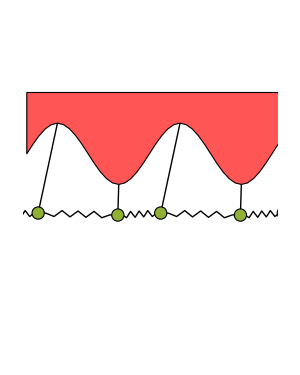
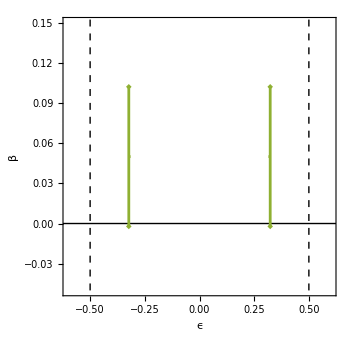
-Graphics- |  | -Graphics- |  | -Graphics-

```mathematica
n0=Max[1,Length[dat]-500];
Monitor[AbsoluteTiming[plots1=Table[
lengths=Riffle[ConstantArray[delta,M/2],ConstantArray[-delta,M/2]];
m=(n-n0);
a=If[(n-n0)<250,amin+(amax-amin)/250*(n-n0),amax];
evals=Cases[Eigenvalues[{A[a,ωd,Δ,q],B[a,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
If[Min[Im[#]&/@evals]<0,thetas=dat[[n,1;;M]],thetas=ConstantArray[0,M]];;
f[x_]:=-delta*Cos[Pi*x/dx];
t=n*2*Pi*0.05/ωd;
z0={0,a*Cos[ωd*t]};
If[MemberQ[First/@Position[Differences[Sign[Differences[dat[[All,1]]]]],2],n],count=count+1;];
count2=Round[(n-n0)/20];
p0=Graphics[{Table[Line[{z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*i,1+lengths[[i]]}}],{i,1,M}],Table[Line[spring[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*(i+1),1+lengths[[i+1]]} -(1+ lengths[[i+1]])*{Sin[thetas[[i+1]]],Cos[thetas[[i+1]]]},10,0.05]],{i,1,M-1}],Line[spring[z0+{dx*M,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx*(M+1),1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],Line[spring[z0+{0,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],EdgeForm[Black],ColorData[97,"ColorList"][[3]],Table[Disk[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},0.1],{i,1,M}],Lighter[Red],Polygon[Join[{{dx/2,z0[[2]]+2}},Table[{x,z0[[2]]+1+f[x]},{x,dx*1/2,dx*(M+1/2),dx/10}],{{dx*(M+1/2),z0[[2]]+2},{dx/2,z0[[2]]+2}}]]},ImageSize->300,PlotRange->{dx*{1/2+0.01,4+1/2+0.01},{-2,3}}];

evals=Cases[Eigenvalues[{A[a,ωd,Δ,q],B[a,ωd,Δ,q]}],u_/;Re[u]>-0.51&&Re[u]<0.51];
p1=Show[ListPlot[{{Re[#],ωd*Im[#]}&/@evals[[1;;2]],{Re[#],ωd*Im[#]}&/@evals[[3;;4]]},PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},ImageSize->350,ImagePadding->{{85,15},{75,10}},Axes->False,Frame->True,FrameLabel->{"ϵ","β"},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Prolog->{Line[{{-1,0},{1,0}}],Dashed,Line[{{0.5,-η/2},{0.5,2*η}}],Line[{{-0.5,-η/2},{-0.5,2*η}}]},PlotStyle->Directive[ColorData[97,"ColorList"][[3]],PointSize[0.08]],PlotMarkers->If[Abs[#[[1]]-#[[2]]]<10^-6&@Abs[Re[evals[[{1,3}]]]],{Graphics[{Polygon[2^(1/2)*{{0,0.05},{0.05,0},{0,-0.05},{-0.05,0}}]},PlotRange->{-1,1}],Graphics[{Polygon[2^(1/2)*{{0,0.05},{0.05,0},{0,-0.05},{-0.05,0}}]},PlotRange->{-1,1}]},{Graphics[{Disk[{0,0},0.05]},PlotRange->{-1,1}],Graphics[{Rectangle[{-0.05,-0.05},{0.05,0.05}]},PlotRange->{-1,1}]}],ImageSize->300,ImagePadding->{{75,10},{75,10}},AspectRatio->1],ListPlot[{{Re[#],ωd*Im[#]}&/@evals1[[{1,3}]],{Re[#],ωd*Im[#]}&/@evals1[[{2,4}]],{Re[#],ωd*Im[#]}&/@evals2[[{2,4}]],{Re[#],ωd*Im[#]}&/@evals2[[{1,3}]]},PlotStyle->Directive[ColorData[97,"ColorList"][[3]],AbsoluteThickness[2]],PlotRange->{{-0.6,0.6},{-η/2,1.5*η}},Joined->True]];
p=Grid[{{p0,Spacer[50],Show[p2,ListPlot[{{ωd/2,a}},PlotStyle->Directive[ColorData[97,"ColorList"][[3]],PointSize[0.04]]]],Spacer[50],p1}},Alignment->Bottom],{n,n0,Length[dat]}];],{N[(n-n0)/(1+Length[dat]-n0)],p}]
plots1[[-1]]
```

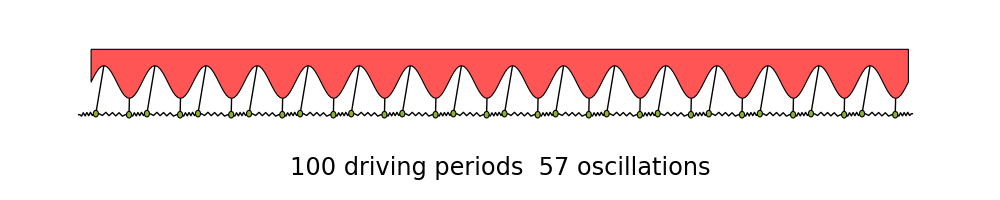

```mathematica
count=0;
n0=Max[1,Length[dat]-2000];
Monitor[AbsoluteTiming[plots2=Table[
lengths=Riffle[ConstantArray[delta,M/2],ConstantArray[-delta,M/2]];
thetas=dat[[n,1;;M]];
f[x_]:=-delta*Cos[Pi*x/dx];
t=n*2*Pi*0.05/ωd;
z0={0,amax*Cos[ωd*t]};
If[MemberQ[First/@Position[Differences[Sign[Differences[dat[[All,1]]]]],2],n],count=count+1;];
count2=Round[(n-n0)/20];
p=Graphics[{Table[Line[{z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*i,1+lengths[[i]]}}],{i,1,M}],Table[Line[spring[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},z0+{dx*(i+1),1+lengths[[i+1]]} -(1+ lengths[[i+1]])*{Sin[thetas[[i+1]]],Cos[thetas[[i+1]]]},10,0.05]],{i,1,M-1}],Line[spring[z0+{dx*M,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx*(M+1),1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],Line[spring[z0+{0,1+lengths[[M]]} -(1+ lengths[[M]])*{Sin[thetas[[M]]],Cos[thetas[[M]]]},z0+{dx,1+lengths[[1]]} -(1+ lengths[[1]])*{Sin[thetas[[1]]],Cos[thetas[[1]]]},10,0.05]],EdgeForm[Black],ColorData[97,"ColorList"][[3]],Table[Disk[z0+{dx*i,1+lengths[[i]]} -(1+ lengths[[i]])*{Sin[thetas[[i]]],Cos[thetas[[i]]]},0.1],{i,1,M}],Lighter[Red],Polygon[Join[{{dx/2,z0[[2]]+2}},Table[{x,z0[[2]]+1+f[x]},{x,dx*1/2,dx*(M+1/2),dx/10}],{{dx*(M+1/2),z0[[2]]+2},{dx/2,z0[[2]]+2}}]],Black, Text[Style[ToString[count2]<>" driving periods  "<>ToString[count]<>" oscillations",24],Scaled[{0.5,0.1}]]},ImageSize->1000,PlotRange->{dx*{1/2+0.01,M+1/2+0.01},{-2,3}}],{n,n0,Length[dat]}]],{N[(n-n0)/(1+Length[dat]-n0)],p}];
plots2[[-1]]
```

```mathematica
If[!DirectoryQ[filebase<>"animation/1/"],CreateDirectory[filebase<>"animation/1/"]]
If[!DirectoryQ[filebase<>"animation/2/"],CreateDirectory[filebase<>"animation/2/"]]
AbsoluteTiming[ParallelDo[Export[filebase<>"animation/1/"<>IntegerString[n,10,4]<>".png",plots1[[n]]], {n,1,Length[plots1]}]]
AbsoluteTiming[ParallelDo[Export[filebase<>"animation/2/"<>IntegerString[n,10,4]<>".png",plots2[[n]]], {n,1,Length[plots2]}]]
```

{31.3261,Null}

{29.6587,Null}